# Introduction to Neural Nets

## LeNet and MNIST

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
```

```mathematica
sample=RandomSample[trainingData,5]
```

{-Graphics-→8,-Graphics-→9,-Graphics-→8,-Graphics-→9,-Graphics-→9}

```mathematica
lenetModel=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
lenetModel[Keys[sample]]
```

{8,9,8,9,9}

```mathematica
NetTrain[NetModel["LeNet"],trainingData,ValidationSet->testData,TargetDevice->"GPU"]
```

NetChain[<>]

```mathematica
lenetTrained=%
```

NetChain[<>]

```mathematica
Information@lenetTrained
```

Net Information

## Layers

```mathematica
last=NetExtract[lenetModel,-1]
```

SoftmaxLayer[<>]

```mathematica
linear=LinearLayer[3,"Input"->2]
```

LinearLayer[<>]

```mathematica
linear=NetInitialize[linear]
```

LinearLayer[<>]

```mathematica
Normal[NetExtract[linear,"Weights"]]
Normal[NetExtract[linear,"Biases"]]
```

{{1.52627,0.798181},{1.20567,0.48485},{-0.0305542,-1.00462}}

{0.,0.,0.}

```mathematica
?*Layer
```

## Net Encoders

```mathematica
imageenc=NetEncoder[{"Image",{12,12},"ColorSpace"->"Grayscale"}]
```

NetEncoder[<>]

```mathematica
imageenc@RandomChoice[Keys[trainingData]]//Normal
```

{{{1.,1.,1.,0.996078,0.988235,0.992157,0.988235,0.988235,0.988235,0.996078,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,0.996078,1.,0.964706,0.580392,0.345098,0.356863,0.380392,0.505882,0.956863,0.996078,0.996078},{0.996078,0.992157,0.988235,0.317647,0.,0.,0.0117647,0.0823529,0.,0.309804,0.996078,0.996078},{0.988235,1.,0.701961,0.,0.0313726,0.247059,0.862745,0.952941,0.254902,0.,0.772549,1.},{0.996078,1.,0.219608,0.,0.498039,1.,1.,1.,0.423529,0.00392157,0.537255,1.},{0.996078,1.,0.141176,0.0470588,0.929412,0.992157,0.992157,0.905882,0.113725,0.,0.596078,1.},{0.996078,1.,0.14902,0.0509804,0.862745,1.,0.94902,0.227451,0.,0.0627451,0.905882,1.},{0.988235,1.,0.627451,0.,0.286275,0.843137,0.466667,0.,0.,0.552941,1.,0.992157},{0.996078,0.992157,0.988235,0.486275,0.,0.,0.,0.,0.427451,0.992157,0.992157,0.996078},{1.,0.996078,1.,1.,0.682353,0.341176,0.294118,0.607843,1.,0.996078,0.996078,1.},{1.,1.,1.,0.996078,1.,1.,1.,1.,0.996078,0.996078,1.,1.}}}

```mathematica
img=-Graphics-;
```

```mathematica
ImageDimensions[img]
```

{150,155}

```mathematica
imageenc[img]//Dimensions
```

{1,12,12}

```mathematica
pool=PoolingLayer[10,"Input"->NetEncoder[{"Image",64}]]
```

PoolingLayer[<>]

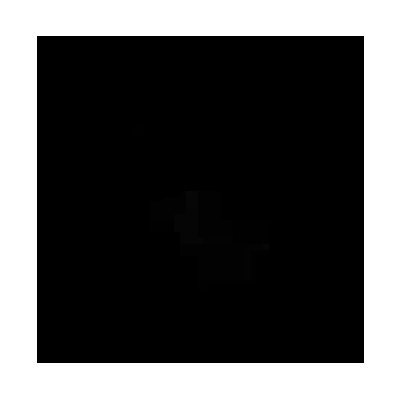
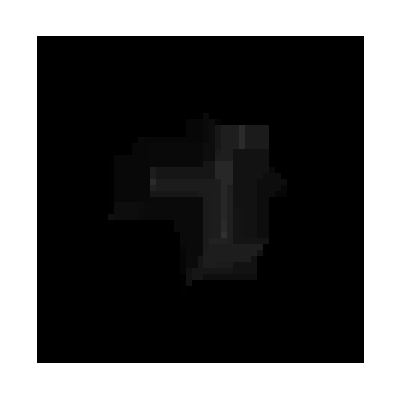
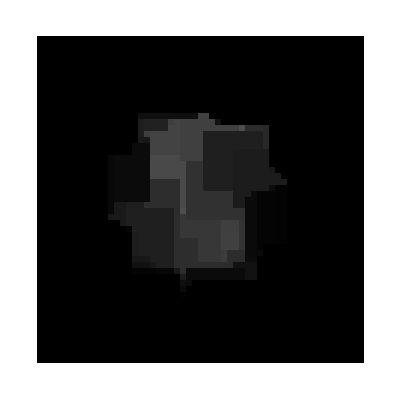

```mathematica
ArrayPlot/@pool[img]
```

```mathematica
img2=-Graphics-;
```

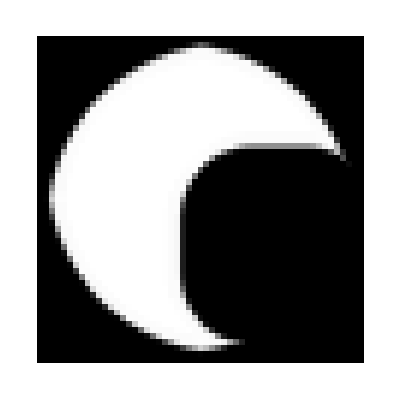
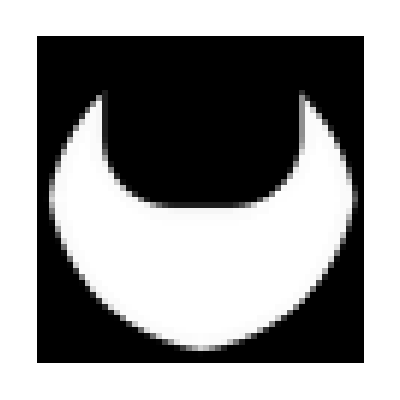
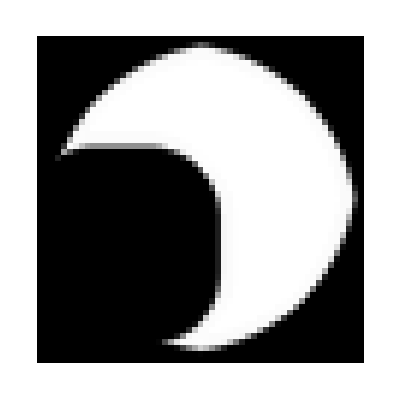

```mathematica
ArrayPlot/@pool[img2]
```

```mathematica
Image[pool[img2],Interleaving->False]
```

-Graphics-

```mathematica
mnistEncoder=NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}]
```

NetEncoder[<>]

```mathematica
trainingData[[1,1]]
```

-Graphics-

```mathematica
ImageDimensions@%
```

{28,28}

## Net Decoders

```mathematica
mnistDecoder=NetDecoder[{"Class",Range[0,9]}]
```

NetDecoder[<>]

```mathematica
mnistDecoder[Join[Table[.3,5],{.8},Table[.4,4]],#]&/@{Nothing,"TopProbabilities",{"Probability",2},"Probabilities","Entropy"}//Column
```

{5→0.8,9→0.4,8→0.4,7→0.4,6→0.4,4→0.3,3→0.3,2→0.3,1→0.3,0→0.3}
0.3
<|0→0.3,1→0.3,2→0.3,3→0.3,4→0.3,5→0.8,6→0.4,7→0.4,8→0.4,9→0.4|>
3.45054

```mathematica
poolBack=PoolingLayer[10,"Input"->NetEncoder[{"Image",64}],"Output"->NetDecoder["Image"]]
```

PoolingLayer[<>]

```mathematica
poolBack[img2]
```

-Graphics-

## Containers

```mathematica
chain=NetChain[{ElementwiseLayer[Sin],ElementwiseLayer[Cos]}]
```

NetChain[<>]

```mathematica
chain[{3.2,-2.3}]
```

{0.998297,0.73461}

```mathematica
Cos[Sin[{3.2,-2.3}]]
```

{0.998297,0.73461}

```mathematica
chain=NetChain[{ElementwiseLayer[Ramp],SoftmaxLayer[]}]
```

NetChain[<>]

```mathematica
chain[{-1,3,2,4}]
```

{0.0120376,0.241783,0.0889468,0.657233}

```mathematica
chain2=NetChain[{ElementwiseLayer[Sin],ElementwiseLayer[Cos],chain}]
```

NetChain[<>]

```mathematica
NetFlatten[chain2]
```

NetChain[<>]

```mathematica
NetGraph[chain2]
```

NetGraph[<>]

```mathematica
NetGraph[NetFlatten[chain2]]
```

NetGraph[<>]

```mathematica
emptyLenet=NetChain[{
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[50,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
FlattenLayer[],
LinearLayer[500],
ElementwiseLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]},
"Input"->mnistEncoder,
"Output"->mnistDecoder]
```

NetChain[<>]

```mathematica
lenet=NetInitialize[emptyLenet]
```

NetChain[<>]

```mathematica
digit=RandomChoice[trainingData]
```

-Graphics-→7

```mathematica
lenet[Keys[digit],"Probabilities"]
```

<|0→0.334158,1→0.199494,2→0.15653,3→0.0075747,4→0.0165687,5→0.0707386,6→0.0426166,7→0.0853378,8→0.0385088,9→0.0484725|>

## Graphs

```mathematica
loss=CrossEntropyLossLayer["Index","Input"->{5}]
```

CrossEntropyLossLayer[<>]

```mathematica
pvector={.8,.05,.05,.05,.05}
```

{0.8,0.05,0.05,0.05,0.05}

```mathematica
loss[<|"Input"->pvector,"Target"->1|>]
```

0.223144

```mathematica
trainingNet=NetGraph[<|"lenet"->lenet,"loss"->CrossEntropyLossLayer["Index"]|>,
{NetPort["Input"]->"lenet"->NetPort["loss","Input"],NetPort["Target"]->NetPort["loss","Target"]}]
```

NetGraph[<>]

```mathematica
trainingNet[<|"Input"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"Target"->{2,4,7,9,8}|>]
```

{0.882252,1.93759,2.3438,2.55826,1.90515}

```mathematica
gradient=trainingNet[<|"Input"->-Graphics-,"Target"->2|>,NetPortGradient[{"lenet",1,"Biases"}]]
```

{-0.100804,-0.0751757,-0.0727627,0.225551,0.,-0.166869,0.0841801,-0.0832312,0.0852701,-0.114436,-0.30109,0.0190691,0.471338,-0.0331595,-0.0874662,-0.076614,-0.169334,-0.197265,-0.240965,-0.187058}

```mathematica
oldBias=Normal@NetExtract[trainingNet,{"lenet",1,"Biases"}];
newBias=oldBias-.1*gradient;
trainingNet2=NetReplacePart[trainingNet,{"lenet",1,"Biases"}->newBias]
```

NetGraph[<>]

```mathematica
test=<|"Input"->-Graphics-,"Target"->2|>
trainingNet[test]
trainingNet2[test]
```

<|Input→-Graphics-,Target→2|>

0.882251

0.821464

## Training

```mathematica
trainAssoc=<|"Input"->Keys[trainingData],"Target"->Values[trainingData]+1|>;
testAssoc=<|"Input"->Keys[testData],"Target"->Values[testData]+1|>;
```

```mathematica
results=NetTrain[trainingNet,trainAssoc,All,ValidationSet->testAssoc,MaxTrainingRounds->5,TargetDevice->"GPU"]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:4690  rounds:5  time:7.8s  examples/s:38646
data | ,,  training examples:60000  validation examples:10000  processed examples:300160  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.07×10^-2  error:0.686%
validation | ,,  loss:3.16×10^-2  error:0.990%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
trainedLenet=NetExtract[results["TrainedNet"],"lenet"]
```

NetChain[<>]

```mathematica
trainedLenet=NetReplacePart[trainedLenet,{"Input"->mnistEncoder,"Output"->mnistDecoder}]
```

NetChain[<>]

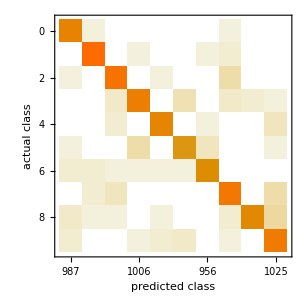
Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (99.010.10) %
Accuracy baseline | (11.350.32) %
Geometric mean of probabilities | 0.969 ± 0.003
Mean cross entropy | 0.0316 ± 0.0031
Single evaluation time | 2.11 ms/example
Batch evaluation speed | 2.54 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[trainedLenet,testData]
```

```mathematica
measurements["Accuracy"]
```

0.9901

```mathematica
measurements["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,CalibrationCurve,CalibrationData,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LinearCalibrationCurve,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}